```mathematica
BlockSVDPowerMethod[A_,V_,s_,precision_]:=(
err=∞;
VV=V;
While[err>precision,
{Q,R}=QRDecomposition[A.VV];
Q=Transpose[Q];
U=Q[[All,1;;s]];

{Q,R}=QRDecomposition[Transpose[A].U];
Q=Transpose[Q];
VV=Q[[All,1;;s]];
Σ1=R[[1;;s,1;;s]];
err=Norm[A.VV-U.Σ1];
];
{U,Σ1,VV}
)
GenerateInitialGuess[s_]:=(
Table[i^2+10*j,{i,600},{j,s}]
)

Cat=ImageData[-Graphics-];
```

```mathematica
CatRed=Cat[[All,All,1]];
Dimensions[CatRed]
```

{600,600}

```mathematica
{251,370}
CatRed[[1,1]]
```

{251,370}

0.960784

```mathematica
SVDThreshold=300;
```

```mathematica
CatGreen=Cat[[All,All,2]];
```

```mathematica
CatBlue=Cat[[All,All,3]];
```

```mathematica
initialGuess=GenerateInitialGuess[SVDThreshold];
precision=0.00001;
SVDCatRed=BlockSVDPowerMethod[CatRed,initialGuess,SVDThreshold,precision];
SVDCatBlue=BlockSVDPowerMethod[CatBlue,initialGuess,SVDThreshold,precision];
SVDCatGreen=BlockSVDPowerMethod[CatGreen,initialGuess,SVDThreshold,precision];



(*SVDCatRed=SingularValueDecomposition[CatRed,SVDThreshold];*)
```

```mathematica
(*SVDCatBlue=SingularValueDecomposition[CatBlue,SVDThreshold];*)
```

```mathematica
(*SVDCatGreen=SingularValueDecomposition[CatGreen,SVDThreshold];*)
Σ =SVDCatRed[[2]];
```

```mathematica
U=SVDCatRed[[1]];
```

```mathematica
VTr=Transpose[SVDCatRed[[3]]];
Dimensions[Σ]
```

{300,300}

```mathematica
Dimensions[U]
```

{600,300}

```mathematica
Dimensions[VTr]
```

{300,600}

```mathematica
x=60;
(s^2+x*s+s*x)*3
```

3 (120 s+s^2)

```mathematica
1107*4
```

4428

```mathematica
SVDCatRedMult=U.Σ .VTr;
```

```mathematica
Image[SVDCatRedMult]
```

-Graphics-

```mathematica
SingValuesRed=Diagonal[Σ];
```

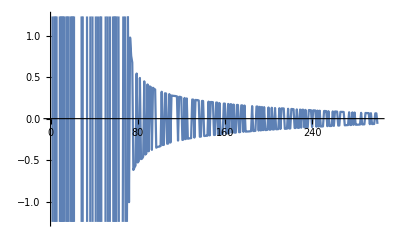

```mathematica
ListLinePlot[SingValuesRed]
```

```mathematica
ΣBlue =SVDCatBlue[[2]];
```

```mathematica
UBlue=SVDCatBlue[[1]];
```

```mathematica
VTrBlue=Transpose[SVDCatBlue[[3]]];

SVDCatBlueMult=UBlue.ΣBlue .VTrBlue;
```

```mathematica
Image[SVDCatBlueMult]
```

-Graphics-

```mathematica
SingValuesBlue=Diagonal[ΣBlue];
```

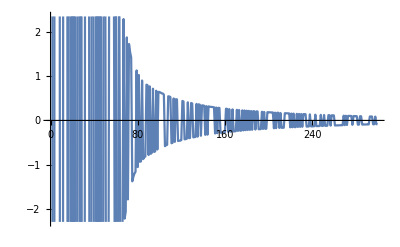

```mathematica
ListLinePlot[SingValuesBlue]
```

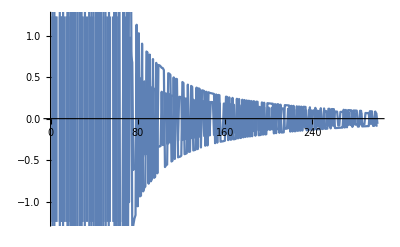

```mathematica
Show[ListLinePlot[SingValuesRed],ListLinePlot[SingValuesBlue]]
```

```mathematica
ΣGreen =SVDCatGreen[[2]];
UGreen=SVDCatGreen[[1]];
```

```mathematica
VTrGreen=Transpose[SVDCatGreen[[3]]];
```

```mathematica
SVDCatGreenMult=UGreen.ΣGreen .VTrGreen;
SingValuesGreen=Diagonal[ΣGreen];
```

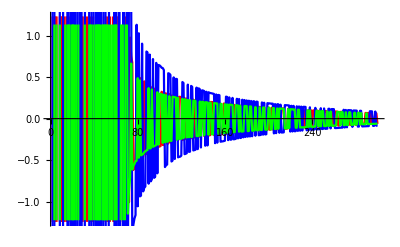

```mathematica
Show[ListLinePlot[SingValuesRed,PlotStyle->Red],ListLinePlot[SingValuesBlue,PlotStyle->Blue],ListLinePlot[SingValuesGreen,PlotStyle->Green]]
```

```mathematica
Image[SVDCatGreenMult]
```

-Graphics-

```mathematica
dim=Dimensions[Cat];
m=dim[[1]];
n=dim[[2]];
FinalSVDCat=Table[0,{i,m},{j,n}];
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
r=SVDCatRedMult[[i,j]];
g=SVDCatGreenMult[[i,j]];
b=SVDCatBlueMult[[i,j]];
FinalSVDCat[[i,j]]={r,g,b};
]
]
```

```mathematica
Image[FinalSVDCat]
```

```mathematica
Export["lady4.jpg",-Graphics-]
```

lady4.jpg

```mathematica
Export["lady2.jpg",-Graphics-]
```

lady2.jpg

```mathematica
Export["lady.jpg",-Graphics-]
```

lady.jpg

```mathematica
Export["example1.png",Plot[Exp[x],{x,0,3}]]
```

example1.png